```mathematica
Manipulate[Plot[f[x],{x,0,2 Pi}],{f,{Sin->Graphics[Disk[]],Cos->"cosine",Tan->"tangent"}}]
```

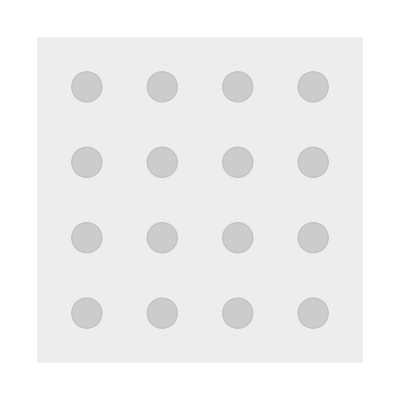

```mathematica
multiwaygraph3[fourcoords, Range[16]/. _Integer->0, fourmoves]
```

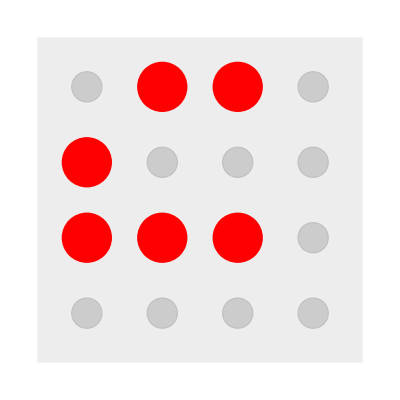
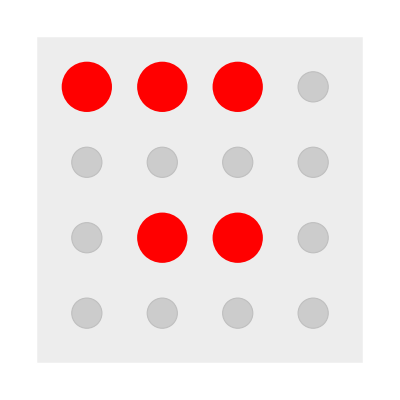
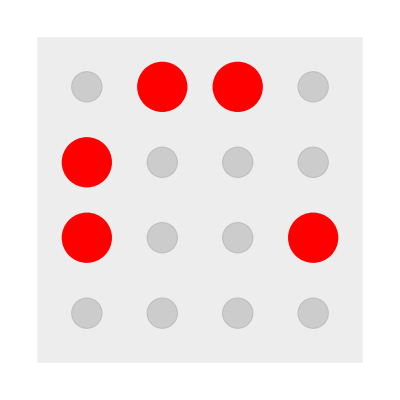
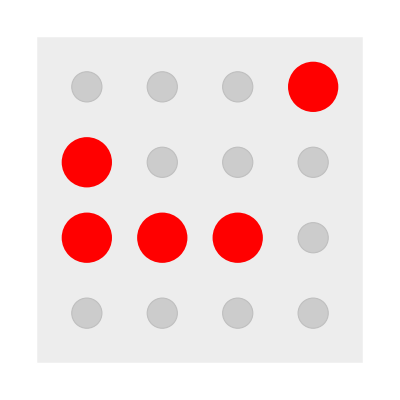
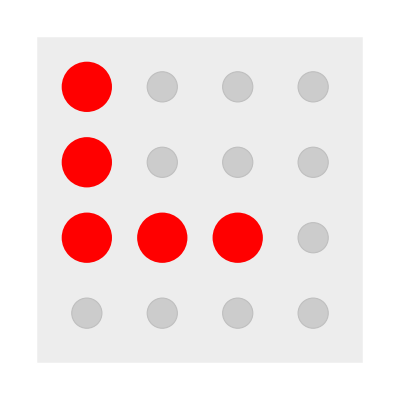
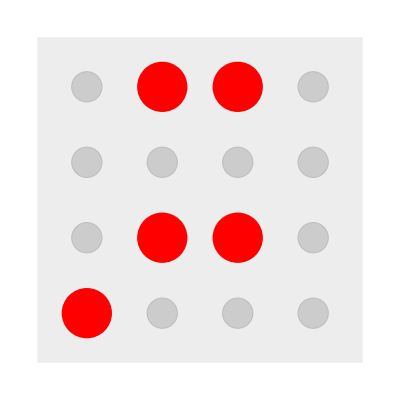
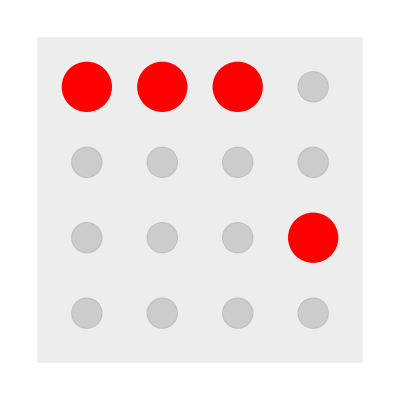
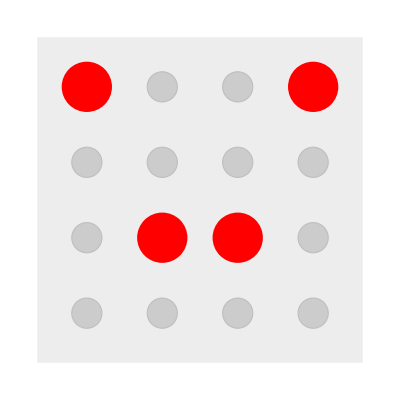
```mathematica
Manipulate[fourFiveGraphHighlight[fivegraph,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2],{{graph,{multiwaygraph3[fourcoords, Range[16]/. _Integer->0, fourmoves],{1,0}} ," "},{{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,{1,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-][[1]]],{-Graphics-,{1,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,1}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]],{-Graphics-,{0,0}}->{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]}}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Outer::heads: Heads List and Symbol at positions 3 and 2 are expected to be the same.

ConvexHullMesh::pts: Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1] should be a non-empty list of points.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

MapThread::mptd: Object Symbol[] at position {2, 1} in MapThread[{{0,1,1,1,0,1,0,0,0,0,«6»}⟦#2⟧/.{1→EdgeForm[None],0→EdgeForm[GrayLevel[«1»]]},{0,1,1,1,0,1,0,0,0,0,«6»}⟦#2⟧/.{1→Red,0→color},Disk[#1,{0,1,1,1,0,1,0,0,0,0,«6»}⟦#2⟧/.{1→Times[«2»],0→Times[«2»]}]}&,{Symbol[],Symbol[]}] has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in Show[ConvexHullMesh[Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1],BaseStyle→Directive[color,EdgeForm[Directive[color,AbsoluteThickness[1]]]]],].

Outer::heads: Heads List and Symbol at positions 3 and 2 are expected to be the same.

ConvexHullMesh::pts: Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1] should be a non-empty list of points.

MapThread::mptd: Object Symbol[] at position {2, 1} in MapThread[{{0,0,1,1,0,0,0,0,0,1,«6»}⟦#2⟧/.{1→EdgeForm[None],0→EdgeForm[GrayLevel[«1»]]},{0,0,1,1,0,0,0,0,0,1,«6»}⟦#2⟧/.{1→Red,0→color},Disk[#1,{0,0,1,1,0,0,0,0,0,1,«6»}⟦#2⟧/.{1→Times[«2»],0→Times[«2»]}]}&,{Symbol[],Symbol[]}] has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in Show[ConvexHullMesh[Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1],BaseStyle→Directive[color,EdgeForm[Directive[color,AbsoluteThickness[1]]]]],].

Outer::heads: Heads List and Symbol at positions 3 and 2 are expected to be the same.

General::stop: Further output of Outer::heads will be suppressed during this calculation.

ConvexHullMesh::pts: Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1] should be a non-empty list of points.

General::stop: Further output of ConvexHullMesh::pts will be suppressed during this calculation.

MapThread::mptd: Object Symbol[] at position {2, 1} in MapThread[{{0,1,1,1,0,1,0,0,0,1,«6»}⟦#2⟧/.{1→EdgeForm[None],0→EdgeForm[GrayLevel[«1»]]},{0,1,1,1,0,1,0,0,0,1,«6»}⟦#2⟧/.{1→Red,0→color},Disk[#1,{0,1,1,1,0,1,0,0,0,1,«6»}⟦#2⟧/.{1→Times[«2»],0→Times[«2»]}]}&,{Symbol[],Symbol[]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ConvexHullMesh[Outer[Plus,Symbol[],{{2/3,2/3},{2/3,-2/3},{-2/3,2/3},{-2/3,-2/3}},1],BaseStyle→Directive[color,EdgeForm[Directive[color,AbsoluteThickness[1]]]]],].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
Partition[Riffle[Table[multiwaygraph3[fourcoords,state,fourmoves],{state, Table[state, {state, Table[getFourCoords[-Graphics-, perm[[1]],perm[[2]]],{perm, options}]}]}],{{1,0},{1,1},{0,1},{0,0}}],2]
```

{{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,{1,0}},{-Graphics-,{1,1}},{-Graphics-,{0,1}},{-Graphics-,{0,0}}}

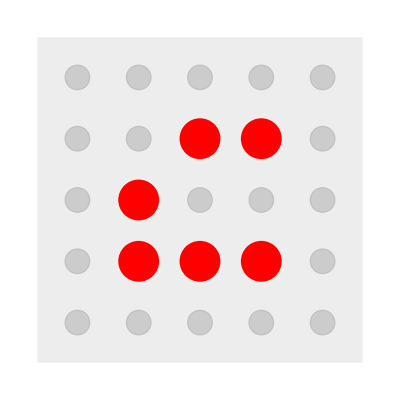
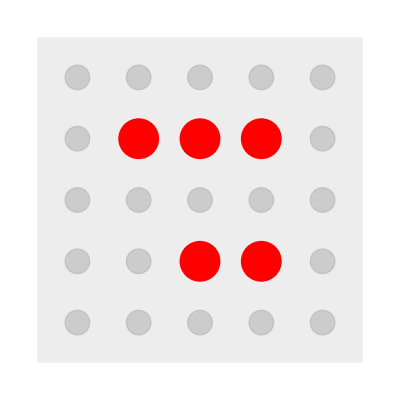
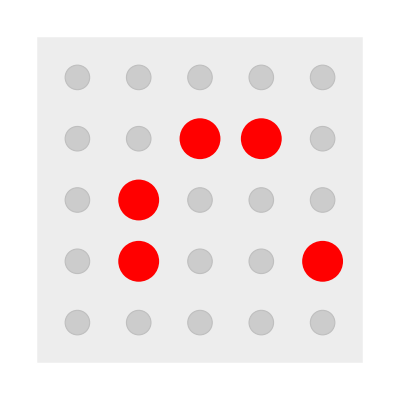
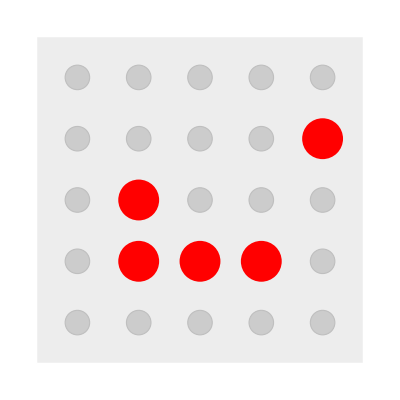
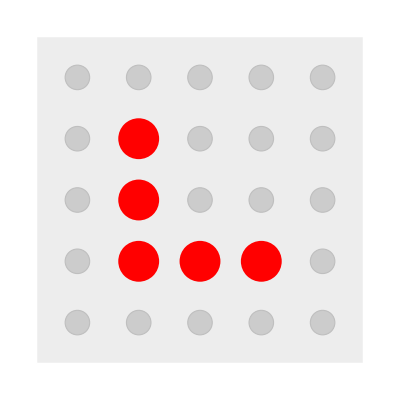
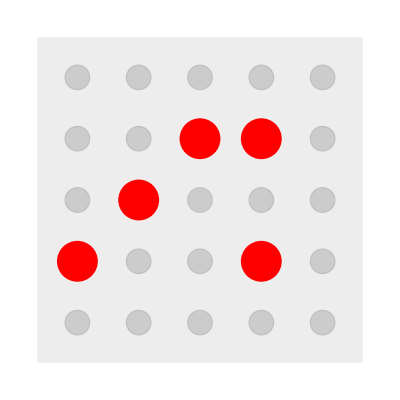
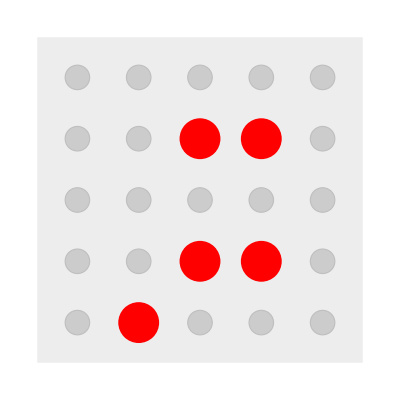
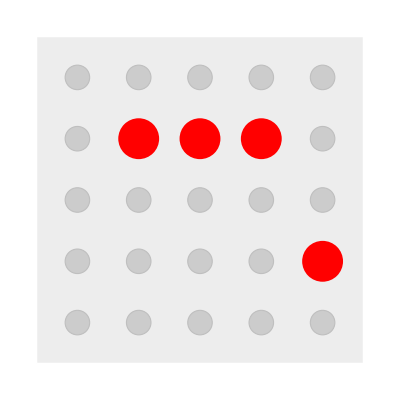
{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[fourFiveGraphHighlight[fivegraph,graph[[1]],graph[[2]][[1]],graph[[2]][[2]],.5,2], {graph,Partition[Riffle[Table[multiwaygraph3[fourcoords,state,fourmoves],{state, Table[state, {state, Table[getFourCoords[-Graphics-, perm[[1]],perm[[2]]],{perm, options}]}]}],{{1,0},{1,1},{0,1},{0,0}}],2]}]
```

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[coordnames[fourcoords]][VertexList[-Graphics-][[1]]]
```

-Graphics-

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

```mathematica
Manipulate[cropGraph[-Graphics-,pins,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{pins,9,2,1,Appearance->"Labeled"},ContinuousAction->False]
```

```mathematica
Manipulate[cropGraph2Way[-Graphics-,max,min,{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}],{max,9,min+1,1,Appearance->"Labeled"},{min,1,max-1,1,Appearance->"Labeled"}, ContinuousAction->False]
```

```mathematica
cropGraph2Way[-Graphics-,3,2,fourcoords]
```

-Graphics-

```mathematica
%//Timing
```

{0.000103,-Graphics-}

```mathematica
Reverse[Range[5,16]]
```

{16,15,14,13,12,11,10,9,8,7,6,5}

```mathematica
Length[VertexList[][[1]]]
```

16

```mathematica
VertexCount[]
```

513

```mathematica
VertexCount[-Graphics-]
```

10

$Aborted

```mathematica
Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Permutations[Join[Range[(7)]/. _Integer->1, Range[2]/. _Integer->0 ]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Permutations[Join[Range[9-holes]/. _Integer->1, Range[holes]/. _Integer->0 ]]]}],{holes, 1,8,1}]
```

```mathematica
holeBoardPerms[2,9]
```

{{1,1,1,1,1,1,3,3,0},{1,1,1,1,1,1,3,0,3},{1,1,1,1,1,3,1,3,0},{1,1,1,1,1,3,1,0,3},{1,1,1,1,1,3,3,1,0},{1,1,1,1,1,3,3,0,1},{1,1,1,1,1,3,0,1,3},{1,1,1,1,1,3,0,3,1},{1,1,1,1,1,0,3,1,3},{1,1,1,1,1,0,3,3,1},{1,1,1,1,3,1,1,3,0},{1,1,1,1,3,1,1,0,3},{1,1,1,1,3,1,3,1,0},{1,1,1,1,3,3,1,0,1},{1,1,1,1,3,3,0,1,1},{1,1,1,1,3,0,3,1,1},{1,1,1,1,0,1,1,3,3},{1,1,1,1,0,1,3,1,3},{1,1,1,1,0,3,1,3,1},{1,1,1,1,0,3,3,1,1},{1,1,1,3,1,3,1,1,0},{1,1,1,3,1,3,1,0,1},{1,1,1,3,1,0,1,1,3},{1,1,1,3,1,0,1,3,1},{1,1,1,3,1,0,3,1,1},{1,1,1,3,3,0,1,1,1},{1,1,1,3,0,3,1,1,1},{1,1,3,1,1,1,3,1,0},{1,1,3,1,1,1,3,0,1},{1,1,3,1,1,1,0,1,3},{1,1,3,1,1,1,0,3,1},{1,1,3,1,1,3,0,1,1},{1,1,3,1,3,1,0,1,1},{1,1,3,1,0,1,3,1,1},{1,1,3,3,1,1,1,1,0},{1,1,3,3,1,1,1,0,1},{1,1,3,0,1,1,1,1,3},{1,1,0,3,1,1,1,3,1}}

```mathematica
holeBoardCoords[threecoords, {1,1,1,1,1,1,3,3,0}]
```

{{1,1}→1,{2,1}→2,{3,1}→3,{1,2}→4,{2,2}→5,{3,2}→6,{2,3}→8,{3,3}→9}

```mathematica
Manipulate[Table[{{"[◼]", "PegSolitaireGraphics"}}[holeBoardCoords[threecoords, perm]][perm],{perm, holeBoardPerms[holes,9]}],{holes, 1,7,1},ContinuousAction->False]
```

```mathematica
multiwaygraph[{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}, {0,1,1,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

-Graphics-

```mathematica
EdgeList[%]
```

{{0,1,1,1,1,1,1,1}->{1,1,1,0,1,0,1,1},{1,1,1,0,1,0,1,1}->{1,0,0,1,1,0,1,1},{1,0,0,1,1,0,1,1}->{0,0,0,0,1,1,1,1},{1,0,0,1,1,0,1,1}->{1,0,1,1,0,0,1,0},{0,0,0,0,1,1,1,1}->{0,0,1,0,0,1,1,0},{1,0,1,1,0,0,1,0}->{0,0,1,0,0,1,1,0},{1,0,1,1,0,0,1,0}->{1,1,0,0,0,0,1,0},{0,0,1,0,0,1,1,0}->{0,0,1,0,1,0,0,0},{0,0,1,0,1,0,0,0}->{0,0,0,0,0,0,0,1}}

```mathematica
VertexList[%]
```

{{0,1,1,1,1,1,1,1},{1,1,1,0,1,0,1,1},{1,0,0,1,1,0,1,1},{0,0,0,0,1,1,1,1},{1,0,1,1,0,0,1,0},{0,0,1,0,0,1,1,0},{1,1,0,0,0,0,1,0},{0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1}}

```mathematica
Count[{0,1,1,1,1,1,1,1},1]
```

7

```mathematica
Count[{{0,1,1,1,1,1,1,1}->{1,1,1,0,1,0,1,1}}[[1]][[1]],1]
```

7

```mathematica
samplegraph = multiwaygraph[{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}, {0,1,1,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}];

Table[HighlightGraph[samplegraph, Table[If[Count[edge[[1]],1]>=i,edge, Nothing], {edge, EdgeList[samplegraph]} ]], {i, Reverse[Range[7]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mgraph = -Graphics-
```

-Graphics-

```mathematica
ListAnimate[Table[HighlightGraph[mgraph, Table[If[Count[edge[[1]],1]>=i,edge, Nothing], {edge, EdgeList[mgraph]} ]], {i, Reverse[Range[Count[VertexList[mgraph][[-1]],1,1],Count[VertexList[mgraph][[1]],1,1]]]}]]
```